Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 10 Sequences
Is the given sequence z_1,z_2,⋯,z_n,⋯ bounded? Convergent? Find its limit points.

1.  z_n=(1+ⅈ)^(2 n)/2^n

```mathematica
Clear["Global`*"]
```

Now that I have followed the s.m. method on problem 3, I will try it on this problem.

```mathematica
Subscript[z, n]=(1+ⅈ)^(2 n)/2^n
```

(1+ⅈ)^(2 n) 2^-n

```mathematica
(1+ⅈ)^2==2 ⅈ
```

True

Which makes the original expression,

```mathematica
(1+ⅈ)^(2 n)/2^n==((2 ⅈ)/2)^n
```

(1+ⅈ)^(2 n) 2^-n==ⅈ^n

Matching the text answer in content. As the text answer points out, ⅈ^n is not convergent, though it is bounded at its lower end by 1. Though I didn’t see it, the text answer informs me that it is also bounded by -1, and by ±ⅈ.

3.  z_n=(n π)/(4+2 n ⅈ)

```mathematica
Clear["Global`*"]
```

This problem is included in the s.m., which looks at two different solution methods. The second solution method seems more straightforward than the first.

```mathematica
Subscript[z, n]=(n π)/(4 +2 n i)
```

(n π)/(4+2 i n)

Multiplying by an identity,

```mathematica
Subscript[z, n](2 n ⅈ)/(2 n ⅈ)==((n π)/(2 n ⅈ))/((4+2 n i)/(2 n ⅈ))
```

True

Working just with the numerator now,

```mathematica
q1=Expand[(n π)/(2 n ⅈ)]
```

-(ⅈ π)/2

Substituting,

```mathematica
-(ⅈ π)/2==(ⅈ π)/(2 ⅈ^2)
```

True

Cancelling and substituting,

```mathematica
(ⅈ π)/(2 ⅈ^2)==π/(2ⅈ)==π/2(1/ⅈ)==π/2(-ⅈ)==-1/2 π ⅈ
```

True

Now working with just the denominator,

```mathematica
(4+2 n ⅈ)/(2 n ⅈ)==2/(n ⅈ)+1
```

```mathematica
-(ⅈ (4+2 ⅈ n))/(2 n)==1-(2 ⅈ)/n (* MMA has its own preference about the format*)
```

And reassembling,

```mathematica
(-1/2 π ⅈ)/(1-(2 ⅈ)/n)
```

```mathematica
-(ⅈ π)/(2 (1-(2 ⅈ)/n)) (*again, the format differs slightly from the s.m.*)
```

```mathematica
Simplify[Limit[-(ⅈ π)/(2 (1-(2 ⅈ)/n)),n->Infinity]]
```

-(ⅈ π)/2

The green answer matches the text answer. The sequence is convergent. And all convergent sequences are bounded, see for instance http://mathonline.wikidot.com/proof-that-convergent-sequences-are-bounded.

5.  z_n=(-1)^n+10 ⅈ

An alternating sequence like this cannot converge. However, it is bounded. The text answer tells me that the two values that it assumes also function as its bounds.

7.  z_n=n^2+ⅈ/n^2

By inspection, this sequence is both unbounded and divergent. The text does not treat boundedness specifically as far as I can see, but it is not a difficult concept to grasp, see e.g. http://www3.ul.ie/cemtl/pdf%20files/cm2/BoundedSequence.pdf

9.  z_n=(3+3ⅈ)^-n

```mathematica
Limit[(3+3 ⅈ)^-n,n->Infinity]
```

0

Since this sequence has a limit of zero, it is convergent, therefore bounded. (I note that a convergent sequence and a convergent series are quite different, because a vanishing general term does not imply that a series is convergent.)

16 - 25 Series
Is the given series convergent or divergent? Give a reason.

17.  Sum[(-ⅈ)^n/Log[n],{n,2,Infinity}]

```mathematica
Clear["Global`*"]
```

Looks like a plot would be useful.

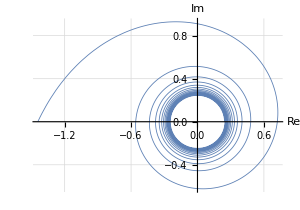

```mathematica
ParametricPlot[{Re[(-ⅈ)^t/Log[t]],Im[(-ⅈ)^t/Log[t]]},{t,2,60},ImageSize->300,AxesLabel->{"Re","Im"},PlotRange->All,AspectRatio->0.7,GridLines->Automatic,PlotStyle->{Thickness[0.002]}]
```

This is an alternating series. According to https://www.dummies.com/education/math/calculus/how-to-determine-whether-an-alternating-series-converges-or-diverges/, the test for convergence of an alternating series consists of 2 parts.

PART 1 The limit of the general term should be zero.

```mathematica
Limit[(-ⅈ)^n/Log[n],n->∞]
```

0

```mathematica
Limit[(-ⅈ)^n/Log[n],n->-∞]
```

0

This series passes part 1 of the test.

PART 2        a_n > a_(n+1)

Referring to the plot, I can see that the series fails part two of the test. (The sense of the plot is clockwise movement.)  By failing the test, the series is shown to be divergent. What about bounds? The series does appear to be bounded. I don’t know how to capture LUB and GLB, but to give some bounds: -1.5+0 ⅈ, 0+ⅈ, 0.8+0 ⅈ, 0-0.7 ⅈ. Incidentally, Mathematica had trouble with this series and did not report it as divergent, even with the command SumConvergence.

19.  Sum[ⅈ^n/(n^2-ⅈ),{n,0,Infinity}]

```mathematica
Clear["Global`*"]
```

Again, to put up a plot,

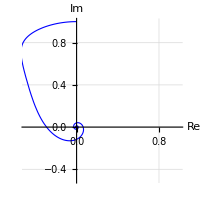
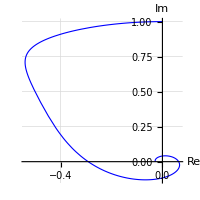

```mathematica
{ParametricPlot[{Re[ⅈ^t/(t^2-ⅈ)],Im[ⅈ^t/(t^2-ⅈ)]},{t,0,60},ImageSize->200,AxesLabel->{"Re","Im"},PlotRange->{-0.5,1},AspectRatio->1,GridLines->Automatic,PlotStyle->{Blue,Thickness[0.004]}],ParametricPlot[{Re[ⅈ^t/(t^2-ⅈ)],Im[ⅈ^t/(t^2-ⅈ)]},{t,0,6},ImageSize->200,AxesLabel->{"Re","Im"},PlotRange->Full,AspectRatio->1,GridLines->Automatic,PlotStyle->{Blue,Thickness[0.004]}]}
```

The right-hand plot above shows a different perspective on the problem function.

```mathematica
Sum[ⅈ^n/(n^2-ⅈ),{n,0,Infinity}]
```

1/2 ⅈ (Hypergeometric2F1[1,-(-1)^(1/4),1-(-1)^(1/4),ⅈ]+Hypergeometric2F1[1,(-1)^(1/4),1+(-1)^(1/4),ⅈ])

This time Mathematica finds the series to be convergent and gives its sum. The text answer gives advice on how to demonstrate convergence, but not on the value of the sum.

21.  Sum[(π+π ⅈ)^(2 n+1)/((2 n+1)!),{n,0,Infinity}]

```mathematica
Clear["Global`*"]
```

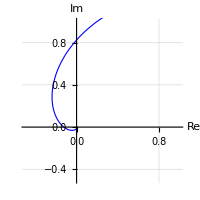
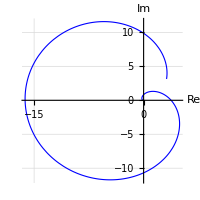

```mathematica
{ParametricPlot[{Re[(π+π ⅈ)^(2 t+1)/((2 t+1)!)],Im[(π+π ⅈ)^(2 t+1)/((2 t+1)!)]},{t,0,60},ImageSize->200,AxesLabel->{"Re","Im"},PlotRange->{-0.5,1},AspectRatio->1,GridLines->Automatic,PlotStyle->{Blue,Thickness[0.004]}],ParametricPlot[{Re[(π+π ⅈ)^(2 t+1)/((2 t+1)!)],Im[(π+π ⅈ)^(2 t+1)/((2 t+1)!)]},{t,0,6},ImageSize->200,AxesLabel->{"Re","Im"},PlotRange->Full,AspectRatio->1,GridLines->Automatic,PlotStyle->{Blue,Thickness[0.004]}]}
```

```mathematica
Sum[(π+π ⅈ)^(2 n+1)/((2 n+1)!),{n,0,Infinity}]
```

-Sinh[π]

The text answer asserts the function’s convergence, but does not reveal the value of the sum.

23.  Sum[((-1)^n(1+ⅈ)^(2 n))/((2 n)!),{n,0,Infinity}]

```mathematica
Clear["Global`*"]
```

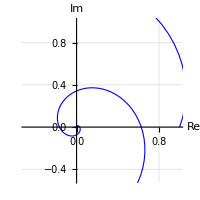
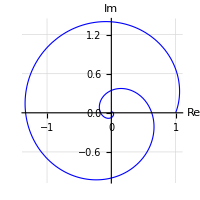

```mathematica
{ParametricPlot[{Re[((-1)^t(1+ⅈ)^(2 t))/((2 t)!)],Im[((-1)^t(1+ⅈ)^(2 t))/((2 t)!)]},{t,0,60},ImageSize->200,AxesLabel->{"Re","Im"},PlotRange->{-0.5,1},AspectRatio->1,GridLines->Automatic,PlotStyle->{Blue,Thickness[0.004]}],ParametricPlot[{Re[((-1)^t(1+ⅈ)^(2 t))/((2 t)!)],Im[((-1)^t(1+ⅈ)^(2 t))/((2 t)!)]},{t,0,6},ImageSize->200,AxesLabel->{"Re","Im"},PlotRange->Full,AspectRatio->1,GridLines->Automatic,PlotStyle->{Blue,Thickness[0.004]}]}
```

```mathematica
Sum[((-1)^n(1+ⅈ)^(2 n))/((2 n)!),{n,0,Infinity}]
```

Cos[1+ⅈ]

The text answer asserts the function’s convergence, but does not reveal the value of the sum.

25.  Sum[ⅈ^n/n,{n,1,Infinity}]

```mathematica
Clear["Global`*"]
```

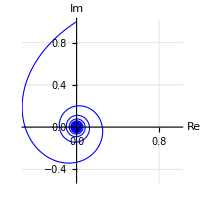
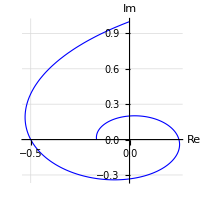

```mathematica
{ParametricPlot[{Re[ⅈ^t/t],Im[ⅈ^t/t]},{t,1,60},ImageSize->200,AxesLabel->{"Re","Im"},PlotRange->{-0.5,1},AspectRatio->1,GridLines->Automatic,PlotStyle->{Blue,Thickness[0.004]}],ParametricPlot[{Re[ⅈ^t/t],Im[ⅈ^t/t]},{t,1,6},ImageSize->200,AxesLabel->{"Re","Im"},PlotRange->Full,AspectRatio->1,GridLines->Automatic,PlotStyle->{Blue,Thickness[0.004]}]}
```

```mathematica
Sum[ⅈ^n/n,{n,1,Infinity}]
```

-Log[1-ⅈ]

The text finds this series to be divergent. Mathematica disagrees. WolframAlpha finds the same answer, but notes that both ratio test and root test are inconclusive. W|A does not tell what criteria it used to find convergence. It does give both a decimal approximation and a series expansion.